# Order of error from truncations

## In the problem, we have done 2 truncations, one in part a, in the integral of Gamma function, and the second in the truncation of the Gaussian integrals, which are special cases of gamma function A proof showing that the relative error decays exponentially can be found here you can visualize the same here by varying the parameters

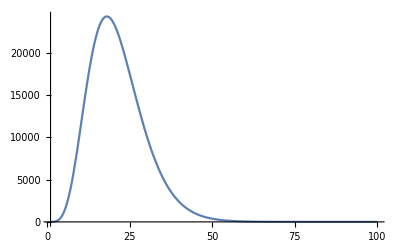

```mathematica
Plot[NIntegrate[x^n Exp[-x] n^6,{x,2n,100n}]/NIntegrate[x^n Exp[-x],{x,0,2n}],{n,1,100}]
```